Input GPDs

```mathematica
fπ[x_]:=1/2*2.6*x^(0.75-1)(1-x)^0.95+1/6*0.21/Beta[0.5+1,8+1] x^(0.5-1)(1-x)^8
gπ[x_]:=-1/6*0.21/Beta[0.5+1,8+1] x^(0.5-1)(1-x)^8
vπ[x_]:=1/2*2.6*x^(0.75-1)(1-x)^0.95
```

```mathematica
h[β_,α_]:=Gamma[2b+2]/(2^(2b+1)Gamma[b+1]^2)*(((1-Abs[β])^2-α^2)^b)/(1-Abs[β])^(2b+1)/.b->2
```

```mathematica
q1[x_,ξ_,t_]:=1/(1+t/6870)(NIntegrate[(h[β,(x-β)/ξ]*fπ[β])/ξ,{β,0,(x+ξ)/(1+ξ)}]+NIntegrate[(h[β,(x-β)/ξ]*gπ[Abs[β]])/ξ,{β,(x-ξ)/(1+ξ),0}])
```

```mathematica
q2[x_,ξ_,t_]:=1/(1+t/6870)NIntegrate[(h[β,(x-β)/ξ]*vπ[β])/ξ,{β,(x-ξ)/(1-ξ),(x+ξ)/(1+ξ)},WorkingPrecision->10]
```

```mathematica
ξ=0.3
```

0.3

```mathematica
NIntegrate[(h[β,(0.1-β)/ξ]*fπ[β])/ξ,{β,0,(0.1+ξ)/(1+ξ)}]+NIntegrate[(h[β,(-0.1-β)/ξ]*gπ[Abs[β]])/ξ,{β,(-0.1-ξ)/(1+ξ),0}]
```

1.6621

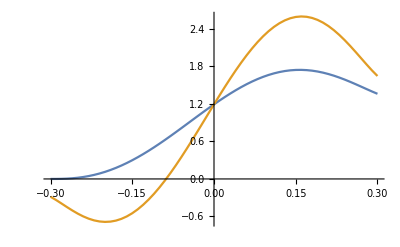

```mathematica
ListLinePlot[{Transpose[{Range[-ξ,ξ,0.01],Table[q1[x,ξ,0],{x,-ξ,ξ,0.01}]}],Transpose[{Range[-ξ,ξ,0.01],Table[NIntegrate[(h[β,(x-β)/ξ]*fπ[β])/ξ,{β,0,(x+ξ)/(1+ξ)}]+NIntegrate[(h[β,(x-β)/ξ]*gπ[Abs[β]])/ξ,{β,(x-ξ)/(1+ξ),0}],{x,-ξ,ξ,0.01}]}]}]
```

```mathematica
Transpose[{Range[-ξ,ξ,0.01],Table[NIntegrate[(h[β,(x-β)/ξ]*fπ[β])/ξ,{β,0,(x+ξ)/(1+ξ)}]+NIntegrate[(h[β,(x-β)/ξ]*gπ[Abs[β]])/ξ,{β,(x-ξ)/(1+ξ),0}],{x,-ξ,ξ,0.01}]}]
```

(-0.3 | -0.284651
-0.29 | -0.335764
-0.28 | -0.391869
-0.27 | -0.448915
-0.26 | -0.503913
-0.25 | -0.5545
-0.24 | -0.598778
-0.23 | -0.635218
-0.22 | -0.662605
-0.21 | -0.679993
-0.2 | -0.68667
-0.19 | -0.682136
-0.18 | -0.666079
-0.17 | -0.638356
-0.16 | -0.598979
-0.15 | -0.548098
-0.14 | -0.485992
-0.13 | -0.413053
-0.12 | -0.329778
-0.11 | -0.236757
-0.1 | -0.134667
-0.09 | -0.0242584
-0.08 | 0.0936488
-0.07 | 0.218177
-0.06 | 0.348396
-0.05 | 0.483332
-0.04 | 0.621976
-0.03 | 0.763288
-0.02 | 0.906207
-0.01 | 1.04966
0. | 1.19255
0.01 | 1.33381
0.02 | 1.47235
0.03 | 1.6071
0.04 | 1.73702
0.05 | 1.86109
0.06 | 1.97832
0.07 | 2.08777
0.08 | 2.18854
0.09 | 2.2798
0.1 | 2.36078
0.11 | 2.43077
0.12 | 2.48917
0.13 | 2.53544
0.14 | 2.56916
0.15 | 2.59002
0.16 | 2.59783
0.17 | 2.59253
0.18 | 2.5742
0.19 | 2.54309
0.2 | 2.49963
0.21 | 2.44441
0.22 | 2.37827
0.23 | 2.30224
0.24 | 2.21763
0.25 | 2.12604
0.26 | 2.02937
0.27 | 1.92993
0.28 | 1.83048
0.29 | 1.73438
0.3 | 1.64597)

```mathematica
NIntegrate[q1[x,ξ,1],{x,-ξ,ξ}]+NIntegrate[q2[x,ξ,1],{x,ξ,1}]
```

NIntegrate::nlim: β = 0.7692307692 (0.3+x) is not a valid limit of integration.

NIntegrate::nlim: β = 0.7692307692 (0.3-1. x) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.01041

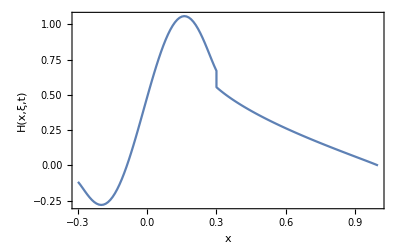

```mathematica
ListLinePlot[Join[Transpose[{Range[-ξ,ξ,0.01],Table[q1[x,ξ,10000],{x,-ξ,ξ,0.01}]}],Transpose[{Range[ξ,1,0.01],Table[q2[x,ξ,10000],{x,ξ,1,0.01}]}]],Frame->True,FrameLabel->{Style["x",15,Black],Style["H(x,ξ,t)",15,Black]}]
```

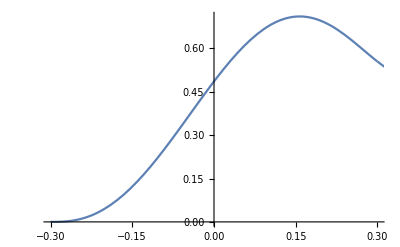

```mathematica
Show[Plot[q1[x,ξ,10000],{x,-ξ,ξ}],Plot[q2[x,ξ,10000],{x,ξ,1}]]
```

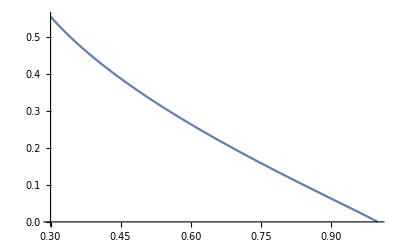

```mathematica
Plot[q2[x,ξ,10000],{x,ξ,1}]
```

```mathematica
Table[NIntegrate[(h[β,(x-β)/ξ]*vπ[β])/ξ,{x,ξ,1},{β,(x-ξ)/(1-ξ),(x+ξ)/(1+ξ)},WorkingPrecision->10]+NIntegrate[(h[β,(x-β)/ξ]*fπ[β])/ξ,{x,-ξ,ξ},{β,0,(x+ξ)/(1+ξ)},WorkingPrecision->10]+NIntegrate[(h[β,(x-β)/ξ]*gπ[Abs[β]])/ξ,{x,-ξ,ξ},{β,(x-ξ)/(1+ξ),0},WorkingPrecision->10],{ξ,0.1,0.5,0.1}]
```

{1.01069048,1.01072235,1.01055078,1.01055282,1.01055563}

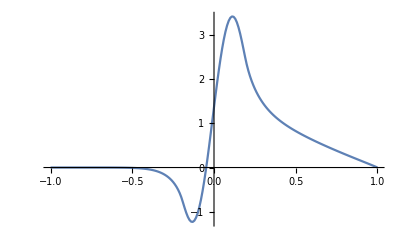

```mathematica
ListLinePlot[Join[Transpose[{Range[-1,-ξ-0.01,0.01],Table[NIntegrate[(h[β,(x-β)/ξ]*gπ[Abs[β]])/ξ,{β,(x-ξ)/(1+ξ),(x+ξ)/(1-ξ)}],{x,-1,-ξ-0.01,0.01}]}],Transpose[{Range[-ξ,ξ,0.01],Table[NIntegrate[(h[β,(x-β)/ξ]*fπ[β])/ξ,{β,0,(x+ξ)/(1+ξ)}]+NIntegrate[(h[β,(x-β)/ξ]*gπ[Abs[β]])/ξ,{β,(x-ξ)/(1+ξ),0}],{x,-ξ,ξ,0.01}]}],Transpose[{Range[ξ+0.01,1,0.01],Table[NIntegrate[(h[β,(x-β)/ξ]*fπ[β])/ξ,{β,(x-ξ)/(1-ξ),(x+ξ)/(1+ξ)}],{x,ξ+0.01,1,0.01}]}]]]
```

Iuput GDA

```mathematica
DA[x_,ξ_,t_]:=1/(1+t/6870)*6x(1-x)*(2ξ-1)
```